# Neighbor overlap

### data reading

```mathematica
p0s={3.825}
```

{3.825}

```mathematica
temperatures={{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001, 0.00067 ,0.0005}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
neighborOverlap=
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/neighborOverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653};
```

```mathematica
neighborOverlapMean=Table[Table[Table[Mean[DeleteCases[Table[neighborOverlap[[p,T,i,2,rec]],{i,Length[neighborOverlap[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[neighborOverlap[[p,T,i,1]]],{i,Length[neighborOverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### plot

```mathematica
N[1/E]
```

0.367879

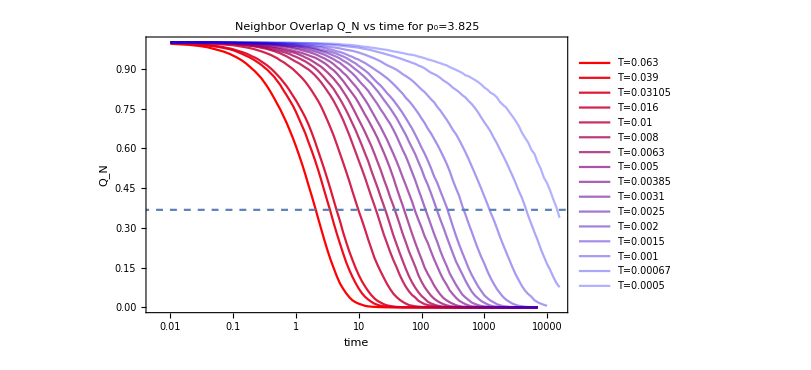

```mathematica
neighborOverlapPlot=Show[Table[
ListLogLinearPlot[Table[Table[{time[[rec]],neighborOverlapMean[[p,T,rec]]},{rec,Length[neighborOverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","Q_N"},ImageSize->600,PlotLabel->"Neighbor Overlap Q_N vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}][[1]],LogLinearPlot[1/E,{x,0.0001,100000},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/neighborOverlap.jpeg",neighborOverlapPlot,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/neighborOverlap.jpeg

```mathematica
tau={2.0633800021033264,3.4662662142411094,4.415641835418887,9.781992106929751,18.870586178193452,26.209843774260023,37.03845794004715,52.34092115893872,77.90370200607369,115.95108859131486,172.5804371204689,256.8669914059181,462.41156668042987,1196.8699596081658,4610.860455987949,14434.572035365063}
```

{2.06338,3.46627,4.41564,9.78199,18.8706,26.2098,37.0385,52.3409,77.9037,115.951,172.58,256.867,462.412,1196.87,4610.86,14434.6}

```mathematica
tauCRoverlap={4.18165032426931,8.808915895509639,12.586410910586487,33.90478836024108,68.84205506885802,95.79491623911186,139.81439488961735,199.29238216380077,307.1398124717621,437.9828929722666,654.6120366652798,941.8800128900245,1673.6040076407396,4228.429123849053,14267.83643147183,43908.53412796377};
```

```mathematica
tauCRSISF={1.5016388282872282,1.30537231329064,1.6086850490671587,9.117479342272413,17.85525517024679,25.702771095873924,35.148879210204,44.034575111551945,65.93056599913932,101.26388862570231,142.2771430149559,216.30204281369626,396.95636115030425,885.77989810605,3331.7713856873056,11914.593480701653};
```

```mathematica
tauOverlapChi4={3.240281741034248,5.893621406466062,8.440263247078125,18.863267352285153,30.464154843193445,35.55407912412377,58.3942074597075,89.7090022629837,135.3965998844829,140.32918832607595,176.05486419287013,227.30754343144173,286.32620197032094};
```

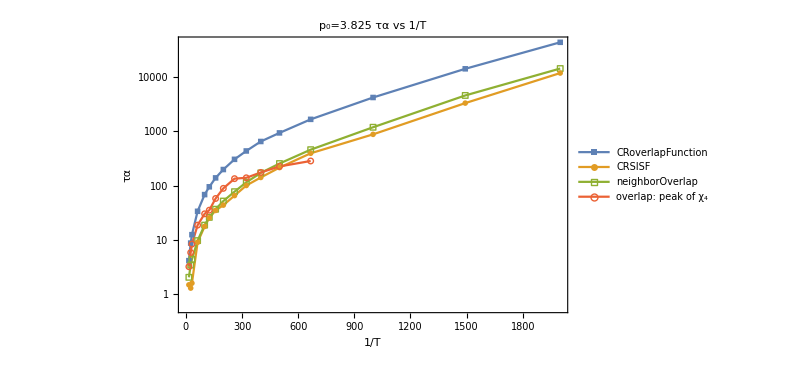

```mathematica
tauAlphaplots=ListLogPlot[{Table[{1/temperatures[[1,T]],tauCRoverlap[[T]]},{T,Length[temperatures[[1]]]}],Table[{1/temperatures[[1,T]],tauCRSISF[[T]]},{T,Length[temperatures[[1]]]}],Table[{1/temperatures[[1,T]],tau[[T]]},{T,Length[temperatures[[1]]]}],Table[{1/temperatures[[1,T]],tauOverlapChi4[[T]]},{T,Length[temperatures[[1]]]-3}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","neighborOverlap","overlap: peak of χ_4"},PlotMarkers->{Style["■",Medium],Style["●",Medium],Style["□",Medium],Style["○",Medium]},ImageSize->600,PlotLabel->"p_0=3.825 τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/updates/05022024/taualpha.jpeg",tauAlphaplots,ImageResolution->800]
```

/home/chengling/Research/updates/05022024/taualpha.jpeg